```mathematica
CondSweep3[x_]:= Exp[-rho*mu*(-(π x^4)/(3 c0)-(c1^3 π x^4)/(3 (c0-c1)^4)+(c1^4 π x^4)/(3 c0 (c0-c1)^4))]
```

```mathematica
fX[x_]:=4x^3Exp[-x^4/theta4]/theta4
Sweep[c0_,c1_]:=-(c0-c1)^3/c1^3
theta4=3*c0/(Pi*rho*mu)
```

(3 c0)/(mu π rho)

```mathematica
fXSweep=CondSweep3[x]*fX[x]/Sweep[c0,c1]
```

-(4 c1^3 ⅇ^(-(mu π rho x^4)/(3 c0)-mu rho (-(π x^4)/(3 c0)-(c1^3 π x^4)/(3 (c0-c1)^4)+(c1^4 π x^4)/(3 c0 (c0-c1)^4))) mu π rho x^3)/(3 c0 (c0-c1)^3)

```mathematica
Simplify[fXSweep]
```

-(4 c1^3 ⅇ^((c1^3 mu π rho x^4)/(3 c0 (c0-c1)^3)) mu π rho x^3)/(3 c0 (c0-c1)^3)

```mathematica
-(4 c1^3 ⅇ^((c1^3 mu π rho x^4)/(3 c0 (c0-c1)^3)) mu π rho x^3)/(3 c0 (c0-c1)^3)
```

-(4 c1^3 ⅇ^((c1^3 mu π rho x^4)/(3 c0 (c0-c1)^3)) mu π rho x^3)/(3 c0 (c0-c1)^3)

```mathematica
fXSweepnew[x_,c0_,c1_]:=-(4 c1^3 ⅇ^((c1^3  x^4)/(theta4 (c0-c1)^3))  x^3)/(theta4(c0-c1)^3)
```

```mathematica
theta4=1
```

1

```mathematica
c0=1
c1=2
```

1

2

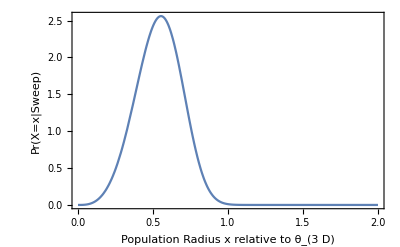

```mathematica
Plot[fXSweepnew[x,c0,c1],{x,0,2}, Frame-> True, FrameLabel-> {Style["Population Radius x relative to θ_(3  D)", Bold, 12],Style["Pr(X=x|Sweep)", Bold, 12] }, RotateLabel->True]
```

```mathematica
Integrate[fXSweepnew[x,c0,c1],{x,0,1}]
```

1-1/ⅇ^8

```mathematica
N[1-1/ⅇ^8]
```

0.999665

```mathematica
c0=1
c1=2
```

1

```mathematica
2
rho=1
mu=1
```

2

1

1

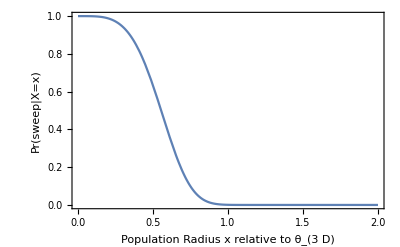

```mathematica
Plot[CondSweep3[x],{x,0,2}, Frame-> True, FrameLabel-> {Style["Population Radius x relative to θ_(3  D)", Bold, 12],Style["Pr(sweep|X=x)", Bold, 12] }, RotateLabel->True]
```

```mathematica
Integrate[CondSweep3[x],{x,0,Infinity}]
```

(3/(7 π))^(1/4) Gamma[5/4]

```mathematica
N[(3/(7 π))^(1/4) Gamma[5/4]]
```

0.550858